First, evaluate Initialisation Cells. The code used to generate the examples can be seen by double clicking the figures, and/or using Cell Properties>Open

Note: the text is an earlier version of the manuscript.

### Abstract

We consider how a population responds to directional selection on standing variation, with no new variation from recombination or mutation.  Initially, there are N individuals with trait values z_1,…,z_N; each individual has a Poisson number of offspring, with mean ⅇ^z_i.  The initial values are drawn from a distribution ψ with variance V_0; we give examples for Laplace or Gaussian distributions.  When selection is weak relative to drift (N √V_0<<1), variance decreases exponentially at rate 1/N; since the increase in mean equals the variance, the expected net change is just NV_0.  This is the same as Robertson’s (1960) for a sexual population, which applies when selection is weak relative to drift. In contrast, when selection is strong relative to drift (N √V_0>>1), we can find the net change by considering the probability of establishment of each allele, using a branching process argument which assumes that each allele is competing independently with the population mean.  Then, if the probability of survival to time t~1/√V_0 is P̃[z], with mean P̄, we find the fittest allele drawn from N P̄ survivors with distribution ψP̃/P̄. When N is large, we find a scaling limit which depends on a single parameter N √V_0; the expected ultimate response is ~√(2log(1.15N √V_0)) for a Gaussian distribution, and ~𝒲(0.36/(N √V_0))/√2) for a Laplace distribution (where 𝒲 is the product log function). This approach also reveals the dynamics of the process, and its variability; we show that in the strong selection regime, the expected genetic variance decreases as t^-3, and we find the distribution of the fitness difference between the top alleles, and hence of the  time to fixation.  We discuss how these results may be related to selection on standing variation that is spread along a linear chromosome.

## Limits to selection on an asexual population

We consider a simple and fundamental problem: how does a large asexual population respond to selection? We assume that selection acts steadily on standing variation, with no input from either mutation or recombination. Thus, the only parameters are the number, N, of individuals, and their fitnesses.

It is surprising that, despite its simplicity, this problem has not (to our knowledge) been addressed before. This may be because population genetics deals mainly with competition between two alleles per locus, whilst quantitative genetics has focussed on genetic variance in sexual populations. Two bodies of work lie closest to the problem studied here. Robertson (1960) showed that the ultimate response to selection on standing variation is a change in mean equal to the genetic population size (i.e. 2N for N diploid individuals) times the change in the first generation. Moreover, he showed that the result implicitly assumes that allele frequencies evolve almost neutrally. Paixao and Barton (2016) extended this result to arbitrary epistasis, and also considered the opposite regime of strong selection. However, these results all apply to a multitude of freely recombining loci in a sexual population,

More recently, there has been a mass of work on fitness waves: the steady increase in fitness of a population as it accumulates beneficial mutations. Such studies were initiated by physicists, seeking simple and familiar problems, and were then studied more rigorously by mathematicians. This work is closely related to the converse problem, of the accumulation of deleterious mutations through Muller’s Ratchet.
However, there seems to have been no  study of the transient response to selection on standing variation, in the absence of mutation or recombination.

Taken literally, the model in question applies to the short-term evolution of an asexual population. Initially, there are N alleles, with some distribution of fitness. If selection were perfectly efficient, the fittest of these would fix, and the its fitness would follow an extreme value distribution. However, even beneficial alleles as likely to be lost in the first generations, and so the winning allele will be the survivor from this early stochastic phase. Note that if the initial fitness distribution is Gaussian, the best allele is unlikely to be more than a few standard deviations above the mean, even if the population is very large; fat-tailed distributions would allow large but erratic responses to selection.

This model may also approximate selection on alleles of a single gene, in a sexual population. When averaged over the genome of an outcrossing eukaryote, selection is likely to be weaker than recombination. However, selection may be concentrated on variation (both regulatory and coding) at a single gene. For example, in Drosophila, a 10kb region would experience recombination at a rate 10^-4; such a region might contain hundreds of segregating sites, and hence an extremely large number of haplotypes. If the selective differences between these were greater than 10^-4, then favourable combinations can increase intact (Sachdeva, 2018). Thus, even though it neglects  recombination,  an asexual model may still be a useful starting point for understanding how selection acts when concentrated on small regions of a sexual genome.

First, we use simulations to confirm that we can rescale time and selective value relative to the standard deviation of fitness; the outcome then depends on a single parameter, N √V_0 (which corresponds to Ns in classical models). When N √V_0 is small, variance in lost mainly by random drift, over ~N generations. Because the increase in mean due to selection equals the genetic variance in fitness (Fisher, 1930), we recover Robertson’s (1960) result, that the ultimate response is N times the change in the first generation, N V_0. However, when N √V_0 is large, variance is lost much faster, through the increase of an exceptionally fit allele that eventually fixes.  We show that in this regime, the outcome can be predicted by finding the value of the fittest survivor at some intermediate time T=t√V_0~1, using a branching process approximation. This approach gives us both the distribution of the ultimate response, and the rate of loss of fitness variance. [results on fixation time and genealogies?]

#### The model

The population consists of N individuals, which reproduce under a Wright-Fisher model; n individual’s chance of being chosen as a parent is proportional to e^z_i, where z_i measures the log. fitness of the i’th allele. Since focus on large N and small z, the diffusion approximation should apply, and details of reproduction should matter only via an effective population size; therefore, we expect that our results would extend to other models of reproduction. For the most part, our analysis assumes that the initial z_i are drawn from a Gaussian distribution; however, we also consider fat-tailed distributions that are much more likely to generate highly fit individuals. Figure 1 shows the mean and standard deviation of the ultimate change in mean, as a function of N √V_0 These are independent of N, following the scaling closely, except for large N √V_0 (top right). For N √V_0 <1, the expected response is close to N √V_0. This is the same relation that Robertson. (1960) found for a sexual population under the infinitesimal model. It can be understood in the same way, by noting that the variance decreases by 1/N per generation, and that the change in mean z per generation is equal to the variance of z. Therefore, the total change in mean is Δ_∞z̄=∑_t V_t=V_0∑_t (1-1/N)^t=N V_0; scaling relative to the initial standard deviation yields Δ_∞z̄/√V_0=N √V_0. This is independent of the initial distribution (Fig. 1b)

Figure 1.  Expected net advance E[Δ_∞z̄]/√V_0 vs. N √V_0, estimated from ?? replicates, for N=100, 400, 1600 (symbols). The left plot shows an initial Gaussian distribution, and the right plot, an exponential distribution. The solid black line shows the prediction N √V_0; colored dashed curves show the expectation over the approximate distribution in Eq. 1, whilst the black dashed curve shows the expectation over the approximate scaling distribution in Eq. 2, which applies in the limit of large N.

|

Because each allele is expected to grow at rate ⅇ^zt, an infinite population would follow a distribution ~ⅇ^zt ψ_0; for an initial Gaussian distribution, this is a Gaussian with constant variance, and mean z̄/√V_0=t √V_0=T, whilst if variance decays only due to drift, then V_t~V_0 ⅇ^(-t/N), and z̄/√V_0~N √V_0(1-ⅇ^(-t/N)). In the small N √V_0 regime (top row), the initial distribution follows this deterministic form, but loses variance at rate 1/N, until after ~N generations, a single variant is fixed.  The expected (scaled) change in mean is Δ_∞z̄/√V_0=N √V_0, but the process is highly stochastic; in the example in Fig. 2a, the mean actually decreases.  In contrast, when N √V_0 is large, the ultimate response is much smaller than N V_0 (compare the smooth curve in Fig. 2b, which shows the prediction if variance were lost only by drift). This is necessarily the case, because the maximum possible change is limited by the fittest of N alleles, which is far less than N standard deviations above the initial mean.  In this regime, the bulk of the distribution stays Gaussian until T~1 (second column in Fig. 2b), at which time one or a few exceptionally fit alleles start to emerge; in this example, the ultimate response is  Δ_∞z̄/√V_0=3.13.

Fig. 2. The evolution of a population of N=10^5 individuals, starting from an initial Gaussian with N √V_0=1, 100, and hence variance V_0=10^-10 or 10^-6 (top, bottom).  The columns show the distributions of z/√V_0 at t=200, 1000, 5000, 25000 generations.  The smooth curve shows a Gaussian with variance that decreases due to drift, as V_0 ⅇ^(-t/N), and mean z̄=V_0 N(1-ⅇ^(-t/N)).

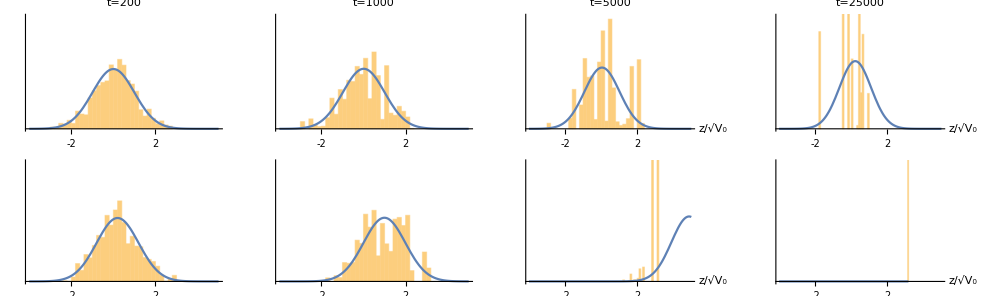

```mathematica
(* runs for large populations can crash *)
smb100=sim[10^5,100,100,1];
smb1=sim[10^5,1,100,1];
Save["sim Jan 2023",sim];
dd[s_,t_,V0_]:=Flatten[ConstantArray[#[[1]]/√V0,#[[2]]]&/@s[[Min[t/100+1,Length[s]]]],1];
gr[s_,t_,n_,V0_,plQ_]:=Show[Histogram[dd[s,t,V0],20,PlotRange->{{-4,5},{0,15000}}],Plot[n/5(ⅇ^(-(z-n √V0(1-Exp[-t/n]))^2/(2Exp[-t/n])))/(√(2π Exp[-t/n])),{z,-4,5}],BaseStyle->baseStyle,AxesLabel->{If[t>2000,"z/√V_0",None],None},Ticks->{{-2,0,2,4},None},PlotLabel->If[plQ,"t="~~ToString[t],None]];
tl={200,1000,5000,25000};GraphicsGrid[{gr[smb1,#,10^5,10^-10,True]&/@tl,gr[smb100,#,10^5,10^-6,False]&/@tl}]
```

We can understand the switch between the two regimes by noting that diversity will be lost through drift in ~N generations, by which time the mean will have advanced by N √V_0 standard deviations (Robertson’s prediction).  However, the fittest surviving allele in a large sample  will be a few standard deviations above the mean; for the moment, we take this to be z~3 √V_0, implying growth by a factor ⅇ^(3N √V_0) by the time drift has eroded diversity.  Therefore, if N √V_0>>1, the fittest allele will dominate before drift has eroded diversity; this is seen in Fig. 2 b, which shows that around T~1, a fit variant becomes visible, and subsequently out-competes all less fit variants. In the following, we make this intuition precise.

#### A branching process approximation

When N √V_0>>1, we can approximate the outcome by following the increase of each allele as an independent branching process, in which an allele of value z_i competes with the mean of the rest of the population, z̄=V_0 t (ignoring the decline in variance due to drift). When selection is weak, we can approximate by a continuous-time diffusion process. Let the probability that an allele with selective advantage s[t], present in n_0 copies at time t_0, will be lost at time t_1 be Q=exp[-n_0P[t_0]]; this form follows from the branching process approximation, which assumes that each of the n_0 copies is lost independently.  The probability of survival of a single copy at t_0 (i.e., n_0=1) is P[t_0], provided that P[t_0]<<1. When selection is weak, the function P[t_0] follows the backwards Kolmogorov equation:

∂_t_0 P = s[t_0] P - P^2/2  with P[t_0]→∞ as t_0->t_1

which has the solution:

P[t_0]=(2g[t_0])/(∫_t_0^t_1 g[τ]ⅆτ)   where g[t]=exp[-∫_t_0^t_1 s[τ]ⅆτ]

The probability that an allele with fixed selective advantage z_i will survive over a time interval t^*=t_1-t_0 is:

P = (2y)/(1-exp[-y T^*])  where  y=z/(√V_0), T^*=t^*√V_0

We can improve this approximation by accounting for the increase in the population mean, such that the allele has net advantage (z-z̄)~(z-V_0 t). Then, the probability of survival to scaled time T^*=t^*√V_0 is:

P[T]=  4 ⅇ^(-((T^*-y)^2)/2)√(V_0/(2π))/  (erf[(T^*-y)/(√2)]+erf[y/(√2)])

This approximation requires that the variance stay close to V_0, and that z>V_0 t, so that the focal allele is fitter than average.  However, the time T^* must be large enough that the fittest allele is unlikely to be lost, once it survives to time t^*. Both assumptions can be satisfied for some T^*~1 if N √V_0>>1.

First, consider the outcome for some initial set of allelic values, z; we rank these such that z_1>z_2>…. There have probability P[z] of surviving until time t; and we now assume that the fittest survivor will ultimately fix. The ultimate response is then the value of the fittest of those surviving at time t^*. The probability that the fittest is z_i, or smaller, is then just:

∏_(j=1)^(i-1) (1-P[z_j])

which is just the probability that all those larger than z_i are lost.

This formula gives the probability distribution of the winner from a given set of values.  The fittest allele over a series of replicates will vary both because of the random initial values, and their subsequent random survival.  Typically, the survival probability will be ~ 2z ~ 2 √V_0, and so we expect that the winner will be ranked ~ 1/(2 √V_0); for any given draw, the best that can be achieved is bounded by the fittest allele - but the actual outcome will almost always be fixation of a much lower ranked allele.

#### The distribution of the ultimate selection response

We now find the distribution of the  selection response, over a random initial draw from a distribution ψ. Then, the distribution of fitnesses, conditional on their survival, is just Pψ/P̄ where P̄=∫Pψⅆz is the mean survival probability. In fact, it is simpler to use the unconditional distribution, which is zero with probability 1-P, and with density Pψ, the allele is not lost and has value z. Thus, we now find the probability that the survivor is less than z as:

F[z] = 𝔼[∏(1-P[z])] ≈ exp[-N∫_z^∞ Pψⅆw]≈ exp[-N √V_0∫_z^∞ P̃ ψⅆw]

The probability of survival is proportional to the selection coefficient, so that we can write P=√V_0 P̃.  Therefore, the key parameter is N √V_0, which under this approximation, only appears through the exponent in Eq. 6.  The probability that the top 1,2,…,k alleles are z_1,…, z_k can be recovered by differentiating F[z]:

f_1(…f)_k exp[-N F_k]   where f[z]=-∂_z F[z], f_j=f[z_j]

Figure 3 compares the CDF of the ultimate response, for the 30 replicates, with the predicted distribution of the fittest survivor (Eq. 6) at T^*= 1, 1.5, 2 (black, blue, purple).  Each panel shows the CDF for N √V_0= 10, 100, 1000. As this parameter increases, the response increases, but only logarithmically; it also becomes more tightly clustered.  The response is about twice as great when the initial distribution is exponential, because the expected value of the extremes of an exponential is much larger than that for a Gaussian. The approximation breaks down for an exponential distribution for N √V_0=1000 (bottom right), because then, with N=10^4,√V_0=0.1, and so the fittest alleles have a very strong selective advantage (~1 for 10s.d.). The approximation still holds for a Gaussian, even for this very large N √V_0 (top right), because the fittest alleles are at only ~3.5sd.

The predicted CDF shifts to lower values as T^* increases, because more alleles are lost, and also because the selective advantage is being diminished by adaptation of the bulk.  T~1 fits best, and the choice of T^* makes less difference as N √V_0 increases.  The crude approximation of Eq. 3 (which neglects the adaptation of the bulk) predicts a higher response, almost independent of T^* (dashed curves).  Thus, whilst our approximation seems only to converge to a value independent of T^*for unreasonably large N √V_0, choosing T^*=1 gives a good approximation to the distribution of response for N √V_0≥10, for both Gaussian and exponential initial distributions.

Figure 3. The cumulative distribution (CDF) of the ultimate response, Δ_∞z̄, compared with various predictions. In each panel, the three sets of curves correspond to N √V_0=10, 100, 1000; the initial distribution is either Gaussian (top) or exponential (bottom). The CDF of 1000 replicate simulations, with N=10^4 (red) is compared with the CDF predicted by calculating the probability of survival to T^*=1, 1.5, 2 (black, blue, purple, solid lines right to left), from Eq. 4. The dashed lines show the same, but using Eq. 3, which neglects the increasing mean of the bulk, and therefore predicts a somewhat higher response; these are almost independent of T, and so the three predictions are hardly distinguishable.

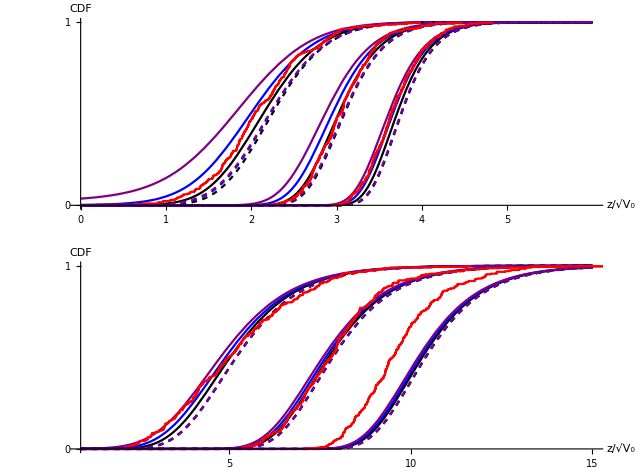

```mathematica
n=10^4;
gr[nv0_]:=Show[cdfPlot[nv0,{1,1.5,2},{Black,Blue,Purple}],cdfPlotCrude[nv0,{1,1.5,2},{Black,Blue,Purple}],
ListLinePlot[listCDF[{#,1}&/@response[n,nv0,100,{300}]],PlotStyle->Red],BaseStyle->baseStyle,Ticks->{{0,1,2,3,4,5},{0,1}},AxesLabel->{"z/√V_0","CDF"},AspectRatio->0.3,AxesOrigin->{0,0},PlotRange->{{0,6},{0,1}}];
grE[nv0_]:=Show[cdfEPlot[nv0,{1,1.5,2},{Black,Blue,Purple}],cdfEPlotCrude[nv0,{1,1.5,2},{Black,Blue,Purple}],
ListLinePlot[listCDF[{#,1}&/@responseE[n,nv0,100,{300}]],PlotStyle->Red],BaseStyle->baseStyle,Ticks->{{0,5,10,15},{0,1}},AxesLabel->{"z/√V_0","CDF"},AspectRatio->0.3];
GraphicsColumn[{Show[gr/@{10,100,1000}],Show[grE/@{10,100,1000}]}]
```

#### A simple approximation for the mean response

We now find simple approximations for the mean response, for both Gaussian and exponential initial distributions. This equals 𝔼[z]=∫_0^∞ z (-∂_z F)ⅆz; integrating by parts, 𝔼[z]=∫_0^∞ (1-F)ⅆz.  When N √V_0 is large, the probability that the fittest surviving allele has value less than z is close to zero for small z, and increases sharply to 1 at some z; thus, 1-F is close to 1 up to this value, and 𝔼[z] can be approximated as the value of z for which exp[-N √V_0∫_z^∞ P̃ ψⅆw]=1/2, or ∫_z^∞ P̃ ψⅆw=log[2]/(N √V_0).  If we use the crude approximation that P[z]=2z, or P̃=2z/√V_0=2y, then for a Gaussian, ∫_z^∞ P̃ ψⅆw=∫_y^∞ 2w (ⅇ^(-w^2/2))/(√(2π))ⅆw=2(ⅇ^(-y^2/2))/(√(2π)). Setting this equal to log[2]/(N √V_0), we have 𝔼[y]≈√(2log[(2N √V_0)/(√(2π)log[2])])≈√(2log[1.15N √V_0]).  For an exponential distribution, the same argument leads to log[2]/(N √V_0)=2(1+y)ⅇ^-y, which has the solution y=𝒲[log[2]/(2ⅇ N √V_0)]-1=𝒲[0.127/(N √V_0)]-1, where 𝒲[α] is the product log function, which is the solution to α=𝒲 ⅇ^-𝒲; this is approximately 1.15log[1/α]. Table 1 show that these approximations are accurate for both exponential and Gaussian initial distributions. Essentially, the mean response to selection is given by finding the expected value of the fittest of N P̄ alleles, where P̄ is the probability of surviving to a time t^*~1/√V_0generations. Surprisingly, this probability can be approximated by 2z, even though this neglects competition from the increasingly well-adapted bulk of the population.

Table 1. Mean and standard deviations of response, compared with predictions assuming T^*=1, for Gaussian and exponential initial distributions;  based on the CDF in Fig. 3 (red, black lines).  The simple predictions, based on setting N √V_0∫P̃ ψⅆw=log[2], are also shown.

```mathematica
tt={#,predSimple[#]//N,Mean[response[10^4,#,100,{300}]],predMean[#,1],StandardDeviation[response[10^4,#,100,{300}]],predSD[#,1]}&/@{10,100,1000};
ttE={#,predSimpleE[#]//N,Mean[responseE[10^4,#,100,{300}]],predMeanE[#,1],StandardDeviation[responseE[10^4,#,100,{300}]],predSDE[#,1]}&/@{10,100,1000};
TableForm[Join[{{"N√V_0","√(2  log[1.15  N SqrtBox[SubscriptBox[V, 0]]])","Δ_∞z̄", "pred Δ_∞z̄","sd", "pred sd"},{"gaussian"}},tt,{{"exponential","𝒲[0.127/(N SqrtBox[SubscriptBox[V, 0]])]-1"}},ttE]]
```

N√V_0 | √(2  log[1.15  N SqrtBox[SubscriptBox[V, 0]]]) | Δ_∞z̄ | pred Δ_∞z̄ | sd | pred sd
gaussian |  |  |  |  | 
10 | 2.21057 | 2.09621 | 2.17294 | 0.576678 | 0.544759
100 | 3.08087 | 3.06818 | 3.06715 | 0.376952 | 0.398229
1000 | 3.75459 | 3.68082 | 3.7501 | 0.329422 | 0.33034
exponential | 𝒲[0.127/(N SqrtBox[SubscriptBox[V, 0]])]-1 |  |  |  | 
10 | 5.18425 | 5.16785 | 5.23704 | 1.74246 | 1.53495
100 | 7.84464 | 7.91232 | 7.95049 | 1.44741 | 1.44911
1000 | 10.4011 | 9.67389 | 10.5336 | 1.27404 | 1.40679

#### Predicting the dynamics

So far, we have focussed on the initial stochastic phase, which determines which allele will ultimately fix. However, the dynamics of this process are more complex, and depend on competition between different alleles as they increase to high frequency.  For example, if two alleles with similar fitnesses survive, then it will take a long time for them to fix; this time is inversely proportional to the fitness difference, which is highly variable.  Nevertheless, this sorting out of alleles with similar fitnesses does not much alter the dynamics of the fitness distribution, simply because these alleles are similar in value.

The deterministic dynamics are simple, even with multiple alleles: given that alleles with value z_i are present in n_i copies, they will grow exponentially in relative abundance, even when common, so that:

n_(i,t) = n_(i,0)ⅇ^(z_i t)/(∑_j n_(0,j)ⅇ^-z_jt)

We can use this relation to predict the state of the population starting at generation τ, ignoring stochastic fluctuations.  Figure 4 shows such predictions, starting at generation τ=0 (when each allele is present in one copy), generation 2, or generation 5 (red, purple, black); these later predictions will vary between replicates due to fluctuations over the first few generations.  The predictions are compared with the observed values (in black), both averaged over replicates.

The mean is predicted well up until scaled time T=t√V_0~2, even ignoring random fluctuations altogether (i.e., starting at τ=0 (red). This is because, although every allele is initially present in one copy, and is most likely soon lost, fitness classes are abundant, and at first evolve deterministically.  However, extrapolating from the first generation overestimates the final change in mean, simply because fitter alleles that are included in the prediction are lost by chance.  Nevertheless, most of this loss occurs very early, so that extrapolating even from generation 5 (blue) only slightly overestimates the final mean.  This is only true on average - individual replicates vary considerably, and their trajectory can only be extrapolated reliably once all relevant alleles are abundant.

Remarkably, a completely deterministic approximation works for the variance (compare red with black lines in the right panels of Fig. 4). Although the variance fluctuates considerably across replicates, the average variance follows a trajectory indistinguishable from an entirely deterministic extrapolation.  Starting from an exponential distribution, the variance increases substantially in the early generations, as the fittest alleles increase rapidly; this is captured by the deterministic extrapolation (lower left in Fig. 4).

Figure 4. Observed values of the mean and variance (left, right), averaged over replicates (black), compared with the deterministic predictions (coloured lines). The top row shows an initial Gaussian, and the second row, an initial exponential. Based on 1000 replicate simulations with N √V_0=100, N=1000, √(V_0=0.1). Predictions are made starting at the observed values at generations τ=0, 2, 5 (red, purple, blue).

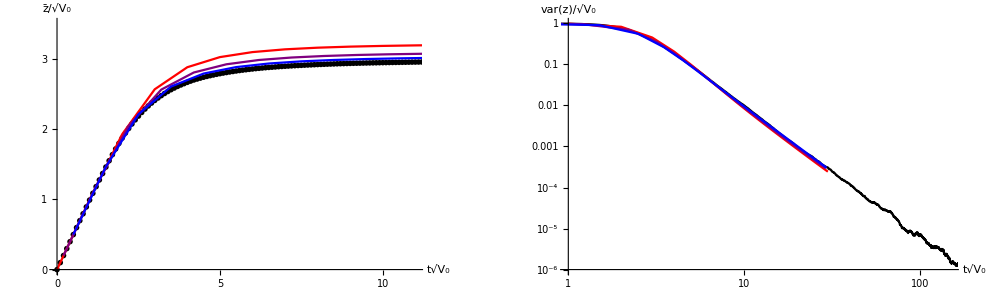

```mathematica
sm=sim[1000,100,{1000}];
v0=0.01;
vt=Map[varz,sm,{2}];vtp=PadRight[#,5000,∅]&/@vt;
meanVt=Mean[DeleteCases[#,∅]]&/@Transpose[vtp];
mm[t_,τ_]:=mm[t,τ]=Mean[meanPred[#,t,τ]&/@sm];
mmt[τ_]:=Table[{t √v0,mm[t,τ]/√v0},{t,τ,300,10}];
mv[t_,τ_]:=mv[t,τ]=Mean[varPred[#,t,τ]&/@sm];
mvt[τ_]:=Table[{t √v0,mv[t,τ]/v0},{t,τ,300,10}];
mt=Map[zbar,sm,{2}];
mtp=PadRight[#,5000,#[[-1]]]&/@mt;
pars={{0,2,5},{Red,Purple,Blue}};v0=0.01;
GraphicsRow[{Show[ListPlot[Transpose[{Range[0,20,0.1],Mean[mtp][[1;;201]]/√v0}],PlotStyle->{Black,PointSize[0.01]},PlotRange->{{0,11},{0,3.5}}],MapThread[ListPlot[mmt[#],Joined->True,PlotStyle->#2,PlotRange->{{0,10},{0,3.5}}]&,pars],
BaseStyle->baseStyle,Ticks->{{0,5,10},{0,1,2,3}},AxesLabel->{"t√V_0","z̄/√V_0"}],
Show[ListLogLogPlot[Transpose[{Range[0.1,500,0.1],Mean[PadRight[#,5000]&/@vt]/v0}],Joined->True,PlotStyle->Black,PlotRange->{{1,150},{10^-6,1}},Ticks->{{1,5,10,50,100},{10^-6,10^-4,0.01,1}//N}],
MapThread[ListLogLogPlot[mvt[#],Joined->True,PlotStyle->#2]&,pars],
BaseStyle->baseStyle,AxesLabel->{"t√V_0","var(z)/√V_0"}]}]
```

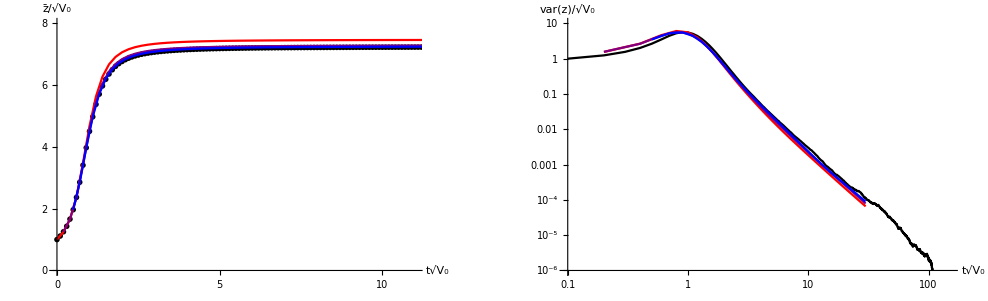

```mathematica
smE=simE[1000,100,{1000}];
v0=0.01;
vtE=Map[varz,smE,{2}];vtpE=PadRight[#,5000,∅]&/@vtE;
meanVtE=Mean[DeleteCases[#,∅]]&/@Transpose[vtpE];
mmE[t_,τ_]:=mmE[t,τ]=Mean[meanPred[#,t,τ]&/@smE];
mmtE[τ_]:=Table[{t √v0,mmE[t,τ]/√v0},{t,τ,300,2}];
mvE[t_,τ_]:=mvE[t,τ]=Mean[varPred[#,t,τ]&/@smE];
mvtE[τ_]:=Table[{t √v0,mvE[t,τ]/v0},{t,τ,300,2}];
mtE=Map[zbar,smE,{2}];
mtpE=PadRight[#,5000,#[[-1]]]&/@mtE;
pars={{0,2,5},{Red,Purple,Blue}};v0=0.01;
GraphicsRow[{Show[ListPlot[Transpose[{Range[0,20,0.1],Mean[mtpE][[1;;201]]/√v0}],PlotStyle->{Black,PointSize[0.01]},PlotRange->{{0,11},{0,8}}],MapThread[ListPlot[mmtE[#],Joined->True,PlotStyle->#2,PlotRange->{{0,10},{0,8}}]&,pars],
BaseStyle->baseStyle,Ticks->{{0,5,10},{0,2,4,6,8}},AxesLabel->{"t√V_0","z̄/√V_0"}],
Show[ListLogLogPlot[Transpose[{Range[0.1,500,0.1],Mean[PadRight[#,5000]&/@vtE]/v0}],Joined->True,PlotStyle->Black,PlotRange->{{0.1,150},{10^-6,10}},Ticks->{{0.5,1,5,10,50,100},{10^-6,10^-4,0.01,1}//N}],
MapThread[ListLogLogPlot[mvtE[#],Joined->True,PlotStyle->#2]&,pars],
BaseStyle->baseStyle,AxesLabel->{"t√V_0","var(z)/√V_0"}]}]
```

```mathematica
vvt=Mean[PadRight[#,5000]&/@vt]/v0;
vvtE=Mean[PadRight[#,5000]&/@vtE]/v0;
rnt=Range[3,30,0.1];
Fit[Log[Transpose[{rnt,#[[31;;301]]}]],{1,t},t]&/@{vvt,vvtE}
```

{2.6639-3.18746 t,1.13571-3.0382 t}

Over later generations (for scaled time T=3 to 30, say), the variance decreases following a power law, as witnessed by the linear decline in the log-log plots of Fig. 4 (right). The decay is ~ t^-3.19for an initial Gaussian, and ~t^-3.04for an initial exponential distribution. One can predict this relation by taking the expectation of the distribution (Eq. 8):

𝔼[var(z)] = 𝔼[(∑_j (z_j-z̄)^2 n_(0,j)ⅇ^-z_jt)/(∑_j n_(0,j)ⅇ^-z_jt)]  where z̄ = (∑_j z_j n_(0,j)ⅇ^-z_jt)/(∑_j n_(0,j)ⅇ^-z_jt)

However, we cannot see how to calculate this, apart from by averaging over random z_i, as in Fig. 4.

#### Relation between the total genetic variance and the change in mean

It is somewhat puzzling that the deterministic prediction accurately predicts the variance, but slightly overestimates the change in mean; yet, the latter should be equal to the total genetic variance, summed over all generations.  Figure 5 shows that  Δ_∞z̄ is, on average, close to ∑_(t=0)^∞ V, their (scaled) means being 2.98, 3.04 respectively.  However, the relationship curves slightly downwards, which may be because with N=1000, √V_0=0.1, selection on the fittest allele is strong, leading to a non-linear relation.

Figure 5. The net change in mean is plotted against the total genetic variance, summed over the whole trajectory; based on 1000 replicates with N √V_0=100, N=1000, starting from a Gaussian.  The red line shows the predicted identity, Δ_∞z̄=∑_(t=0)^∞ V_t, whilst the orange line shows the best quadratic fit, constrained to go through the origin: Δ_∞z̄=1.14∑_t V_t-0.05(∑_t V_t)^2.

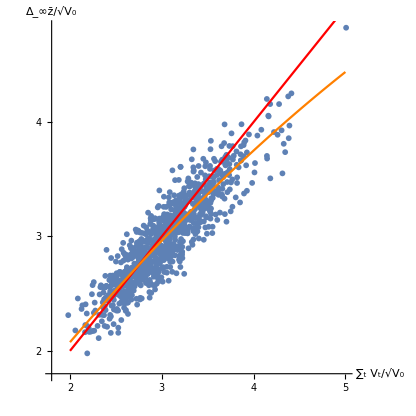

{0.0500376+0.818199 z,0.979848 z,1.13815 z-0.0501383 z^2}

```mathematica
tvt=(Total/@vt)/0.1;
dz=sm[[All,-1,1,1]]/0.1;
tt=Transpose[{tvt,dz}];
ft1=Fit[tt,{z},z];ft2=Fit[tt,{z,z^2},z];
Show[ListPlot[tt,AxesOrigin->{1.8,1.8},PlotStyle->PointSize[0.01]],Plot[{z,ft2},{z,2,5},PlotStyle->{Red,Orange}],AspectRatio->1,BaseStyle->baseStyle,AxesLabel->{"∑_t V_t/√V_0","Δ_∞z̄/√V_0"},Ticks->{{2,3,4,5},{2,3,4,5}}]
{ft0,ft1,ft2}
```

#### Robertson’s argument

I realise that I have been conflating two arguments under “Robertson 1960”. The first is the QG argument under the infinitesimal model: the genic variance decays as V0(1-F), where F is the IBD under the pedigree.  The change in mean equals the addditive genetic variance plus noise, and so includes three sources of variation: fluctuation in F due to the random pedigree; fluctuation in genetic variance around the genic variance, due to random LD (under the infinitesimal model, random sampling of parents); and random variation in the mean around the expected change, proportional to genetic variance.

As I recall, Robertson (1960) hardly mentions this argument, which I guess he took to be obvious.  Rather, he focuses on fixation probability at a single locus, and finds the expected ultimate change due to that one locus as proportional to (P[p0]-p0).  This fixation probability is derived (by Kimura) from the diffusion, and so is valid for large p0, and not just in the branching process phase.  However, otherwise the argument is rather similar to ours, and is really just treating two alleles, rather than a continuum of allelic values.  Maybe this is a way to better connect

#### Timing

```mathematica
Dynamic[rep]
```

The Timing given here is 20 times longer than it actually took - mysterious....

```mathematica
Timing[sm=sim[1000,80,{1000}];]
```

{31.7716,Null}

```mathematica
Timing[sm2=sim[10^4,80,100,{100}];]
```

{670.057,Null}

```mathematica
Timing[sm2=sim[10^4,81,{100}];]
```

{772.928,Null}

```mathematica
{Mean[Length/@sm],Mean[Length/@sm2]}//N
```

{328.645,3358.18}

## Definitions

#### baseStyle

```mathematica
baseStyle::usage="baseStyle  gives the default style";
baseStyle={FontFamily->"Times",FontSize->14};
```

#### zbar, varz

```mathematica
zbar::usage="zbar[{{z_1,n_1},…}] gives the mean trait value";
varz::usage="varz[{{z_1,n_1},…}] gives the variance of trait value";
zbar[pop_List]:=(pop[[All,1]].pop[[All,2]])/Total[pop[[All,2]]];
varz[pop_List]:=Module[{zb=zbar[pop]},(((pop[[All,1]]-zb)^2).pop[[All,2]])/Total[pop[[All,2]]]];
```

#### traj, pos

```mathematica
traj::usage="traj[{{{z_1,n_1},…},…},z] gives the trajectory through time of the allele with value z. traj[{{{z_1,n_1},…},…},z,δ] counts every δ generations";
traj[pop_List,z_]:=Module[{pp=Position[pop,z]},
Extract[pop,{#[[1]],#[[2]],2}]&/@pp];
traj[pop_List,z_,δ_Integer]:=Module[{pp=Position[pop[[1;;-1;;δ]],z]},
Extract[pop[[1;;-1;;δ]],{#[[1]],#[[2]],2}]&/@pp];
```

```mathematica
pos::usage="pos[z,{{{z_1,n_1},…},…}] lists the replicates which ultimately fix allele z; assumes that all replicates run until fixation";
pos[z_,pl_List]:=Flatten[Position[pl[[All,-1,1,1]],z]];
```

#### iter, iterN

```mathematica
iterN::usage="iterN[{{z_1,n_1},…}] uses a multinomial distribution to iterate the population, using WF sampling with fitnesses ⅇ^z. This is much slower than iter for large # of types, but is faster for less than ~20 types";
iterN[pop_List]:=Module[{n=Total[pop[[All,2]]],z=pop[[All,1]],w},
time+=1;w=pop[[All,2]] ⅇ^z;
DeleteCases[Transpose[{z,RandomInteger[MultinomialDistribution[n,w/Total[w]]]}],{_,0}]];
```

```mathematica
iter::usage="iter[{{z_1,n_1},…}] randomly samples to iterate the population, using WF sampling with fitnesses ⅇ^z. This is much faster than iterN for large # of types, but is slower for less than ~20 types";
iter[pop_List]:=Module[{n=Total[pop[[All,2]]],z=pop[[All,1]]},
time+=1;Sort[Tally[RandomChoice[(pop[[All,2]] ⅇ^z)->z,n]]]];
```

```mathematica
time=0;iter[{{0,10},{0.1,20}}]
```

{{0,9},{0.1,21}}

#### makeSim, nAlleles, time

```mathematica
time::usage="time tracks the progress of the simulation";
nAlleles::usage="nAlleles tracks the # of surviving alleles";
makeSim::usage="makeSim[z_0,k] simulates a population, of the form {{z_1,n_1},…}, starting with one copy of each allele. Uses random sampling when nAlleles>k, and the multinomial otherwise. makeSim[z_0,n_0,k] allows any starting frequencies";
makeSim[z0_List,k_]:=Module[{pop0={#,1}&/@z0},
time=0;
NestWhileList[(nAlleles=Length[#];If[nAlleles>k,iter[#],iterN[#]])&,pop0,Length[#]>1&]];
makeSim[z0_List,n0_List,k_]:=Module[{pop0=Transpose[{z0,n0}]},
time=0;
NestWhileList[(nAlleles=Length[#];If[nAlleles>k,iter[#],iterN[#]])&,pop0,Length[#]>1&]];
```

#### Pf

```mathematica
Pf::usage="Pf[z/√V_0,t√V_0,V_0] gives the probability of survival to time t. Pf[z] is the probability of ultimate survival, with fixed log fitness z. Pf[z/√V_0,t√V_0] gives Pf/√V_0, which is very accurate for V_0 small. For large y, small T, this tends to 2y.  Pf[s] gives the survival probability for a simple branching process, with fitness ⅇ^s";
Pf[y_,T_,V0_]:=ⅇ^(y T-T^2/2)/(1+(ⅇ^(y^2/2))/4 √((2 π)/V0)Erf[(y-T)/(√2),y/(√2)]);
Pf[y_,T_]:=4/(√(2π))ⅇ^(-(T-y)^2/2)/Erf[(y-T)/(√2),y/(√2)];
Pf[y_]:=ⅇ^-y (ⅇ^y+ProductLog[-ⅇ^(-ⅇ^y+y)]);
```

```mathematica
Pfc::usage="Pfc[z/√V_0,t√V_0] gives Pf/√V_0, using the crude approximation 2y/(1-ⅇ^(-y T)).  ";
Pfc[y_,T_]:=2y/(1-ⅇ^(-y T));
```

The sum of erf[] in the denominator diverges as ⅇ^(-y^2)for large y, but this cancels with the numerator. Thus, there are numerical instabilities beyond y~8.  The obvious solution is to use the series expansion for erf[], but this converges slowly (as ~ 1/y).  Alternatively, we can write:

P[y,T]=2/∫_(y-T)^y exp[-1/2(w^2-θ^2)]ⅆw   where θ=y-T

This is not actually necessary: Erf[z_0,z_1] gives the difference between two Erf[].

#### Pr, Pk, Pka, Pkaa

```mathematica
Pr::usage="Pr[z] is the integral of a standard normal";
Pr[z_]:=1/2 Erfc[-z/(√2)];
```

```mathematica
Pk::usage="Pk[z,k,n] is the chance that the k'th largest value is z, given n samples from a standard Gaussian";
Pkaa::usage="Pkaa[z,k,n] is the chance that the k'th largest value is z, given n samples from a standard Gaussian, and using the asymptotic form for large z";
Pk[z_,k_Integer,n_Integer]:=n Binomial[n-1,k-1](ⅇ^(-z^2/2))/(√(2π))(1-Pr[z])^(k-1)Pr[z]^(n-k);
Pkaa[z_,k_Integer,n_Integer]:=n Binomial[n-1,k-1](2π)^(-k/2)z^(-(k-1))Exp[-k z^2/2-(n-k)(ⅇ^(-z^2/2))/(z √(2π))];
```

#### coalesce, coalTime

```mathematica
coalesce::usage="coalesce[{n_1,…,n_T},k] iterates back, tracking the # of ancestors pf a sample of k";
coalesce[nl_List,k_Integer]:=FoldList[Length[Union[RandomChoice[Range[#2],#1]]]&,k,Reverse[nl]];
```

```mathematica
coalTime::usage="coalTime[{k_0,…,1}] gives the time to coalescence";
coalTime[cl_List]:=Position[cl,1][[1,1]];
```

#### Timings

Using a multinomial is much slower, unless there are fewer than ~30 haplotypes

```mathematica
TableForm[Prepend[{Length[pl2[[#]]],Timing[iter[pl2[[#]]];][[1]],Timing[iterN[pl2[[#]]];][[1]]}&/@{1,10,100,2000,8000},{"#","RandomChoice","Multinomial"}]]
```

# | RandomChoice | Multinomial
100000 | 0.076015 | 197.59
17203 | 0.041584 | 47.5363
1937 | 0.019117 | 5.81485
72 | 0.050323 | 0.256052
3 | 0.031564 | 0.001154

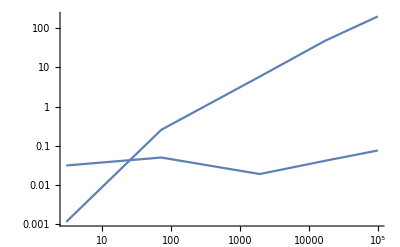

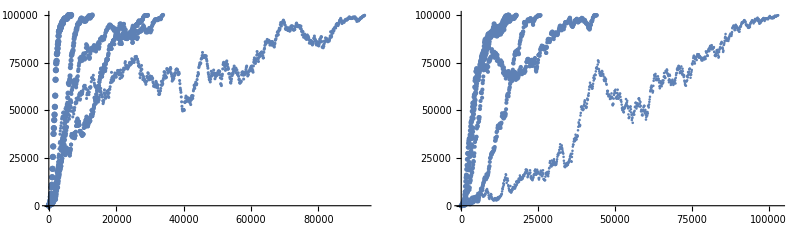

```mathematica
Show[ListLogLogPlot[{{100000, 0.076015}, {17203, 0.041584}, {1937, 0.019117}, {72, 0.050323}, {3, 0.031564}},Joined->True],ListLogLogPlot[{{100000, 197.589991}, {17203, 47.536342}, {1937, 5.814847}, {72, 0.256052}, {3, 0.001154}},Joined->True],PlotRange->All]
```

#### Pb, Pbn

```mathematica
Pb::usage="Pb[T] gives the mean survival probability at T=t√V_0, scaled by √V_0, assuming that values are drawn from a Gaussian, and taght the bulk adapts at rate V_0t.";
Pbn::usage="Pbn[T] gives the mean survival probability at T=t√V_0, scaled by √V_0, assuming that values are drawn from a Gaussian, and that the bulk does not adapt.";
Pb[T_]:=NIntegrate[(ⅇ^(-y^2/2))/(√(2π))Pf[y,T],{y,-∞,∞}];
Pbn[T_]:=NIntegrate[(ⅇ^(-y^2/2))/(√(2π))(2y)/(1-ⅇ^-yT),{y,-∞,∞}];
```

These are the mean survival probabilities to time T, with and without adaptation of the bulk:

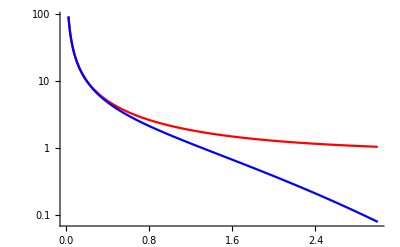

```mathematica
LogPlot[{Pbn[T],Pb[T]},{T,0,3},PlotStyle->{Red,Blue}]
```

#### cdf, cdfc, predMean, predSD

```mathematica
cdf::usage="cdf[T] stores an interpolation function cdf[T][y] for the CDF of the distribution of y=z/√V_0 amongst survivors at time T=t√V_0, assuming an initial Gaussian.  Exp[-N√V_0 cdf[T][y]] gives the CDF of the fittest of N survivors. ";
cdf[T_]:=cdf[T]=Interpolation[Table[{y,NIntegrate[(ⅇ^(-w^2/2))/(√(2π))Pf[w,T],{w,y,∞}]},{y,-3,20,0.1}]];
```

```mathematica
cdfc::usage="cdfc[T] stores an interpolation function cdfc[T][y] for the CDF of the distribution of y=z/√V_0 amongst survivors at time T=t√V_0, assuming an initial Gaussian.  Exp[-N√V_0 cdfc[T][y]] gives the CDF of the fittest of N survivors. Uses the crude approximation Pf=2y/(1-ⅇ^-yT)], and should be used with Exp[-N√V_0 cdfc[T][y]]  ";
cdfc[T_]:=cdfc[T]=Interpolation[Table[{y,NIntegrate[(ⅇ^(-w^2/2))/(√(2π))Pfc[w,T],{w,y,∞}]},{y,-3,20,0.1}]];
```

```mathematica
predMean::usage="predMean[N√V_0,T] predicts the mean response, based on cdf[T]";
predMean[nv0_,T_]:=Module[{y},NIntegrate[1-Exp[-nv0 cdf[T][y]],{y,0,20}]];
```

```mathematica
predSD::usage="predSD[N√V_0,T] predicts the SD of the response, based on cdf[T]";
predSD[nv0_,T_]:=Module[{y,yb=predMean[nv0,T]},
√(yb^2+NIntegrate[2(y-yb)(1-Exp[-nv0 cdf[T][y]]),{y,0,20}])];
```

#### cdfE, cdfcE

```mathematica
cdfE::usage="cdfE[T] stores an interpolation function cdfE[T][y] for the CDF of the distribution of y=z/√V_0 amongst survivors at time T=t√V_0, assuming an initial exponential.  Exp[-N√V_0 cdfE[T][y]] gives the CDF of the fittest of N survivors.  ";
cdfE[T_]:=cdfE[T]=Interpolation[Table[{y,NIntegrate[ⅇ^-w Pf[w,T],{w,y,∞}]},{y,0,20,0.1}]];
```

```mathematica
cdfcE::usage="cdfcE[T] stores an interpolation function cdfcE[T][y] for the CDF of the distribution of y=z/√V_0 amongst survivors at time T=t√V_0, assuming an initial exponential.  Exp[-N√V_0 cdfcE[T][y]] gives the CDF of the fittest of N survivors. Uses the crude approximation Pf=2y/(1-ⅇ^-yT)], and should be used with Exp[-N√V_0 cdfcE[T][y]]  ";
cdfcE[T_]:=cdfcE[T]=Interpolation[Table[{y,NIntegrate[ⅇ^-w Pfc[w,T],{w,y,∞}]},{y,0,20,0.1}]];
```

```mathematica
predMeanE::usage="predMeanE[N√V_0,T] predicts the mean response, based on cdfE[T]";
predMeanE[nv0_,T_]:=Module[{y},NIntegrate[1-Exp[-nv0 cdfE[T][y]],{y,0,20}]];
```

```mathematica
predSDE::usage="predSDE[N√V_0,T] predicts the SD of the response, based on cdfE[T]";
predSDE[nv0_,T_]:=Module[{y,yb=predMeanE[nv0,T]},
√(yb^2+NIntegrate[2(y-yb)(1-Exp[-nv0 cdfE[T][y]]),{y,0,20}])];
```

#### drawTop, listCDF

```mathematica
drawTop::usage="drawTop[N√V_0,T,k] draws the k fittest values from the survivors of N at scaled time T";
drawTop[nv_,T_,k_Integer]:=Module[{zm,y},
zm=RandomVariate[ProbabilityDistribution[{"CDF",Exp[-nv cdf[T][y]]},{y,0,10}]];
NestList[RandomVariate[ProbabilityDistribution[{"CDF",Exp[-nv(cdf[T][y]-cdf[T][#])]},{y,0,#}]]&,zm,k-1]];
```

```mathematica
listCDF::usage="listCDF[{{z_1,n_1},…}] returns the CDF, in the form {{z_1,0},{z_1,1/N},…,{z_-1,1-1/N},{z_-1,1}}";
listCDF[znl_List]:=Module[{zl=First/@znl,nl=Last/@znl,cnl},
cnl=FoldList[Plus,0,nl];cnl=cnl/Last[cnl];
Sort[Join[Transpose[{zl,Drop[cnl,1]}],Transpose[{zl,Drop[cnl,-1]}]]]];
```

#### cdfPlot, cdfPlotCrude

```mathematica
cdfPlot::usage="cdfPlot[N√V_0T^*,c] plots the predicted CDF, in style c. cdfPlot[N√V_0{T^*,…},{c,…}] superimposes several predictions.";
cdfPlotCrude::usage="cdfPlotCrude[N√V_0T^*,c] plots the predicted CDF, ignoring adaptation of the bulk, in style c. cdfPlotCrude[N√V_0{T^*,…},{c,…}] superimposes several predictions.";
cdfPlot[nv0_,T_?NumberQ,c_]:=Plot[Exp[-nv0 cdf[T][y]],{y,0,6},PlotStyle->c,PlotRange->{{0,6},{0,1}}];
cdfPlot[nv0_,T_List,c_List]:=Show[MapThread[cdfPlot[nv0,##]&,{T,c}]];
cdfPlotCrude[nv0_,T_,c_]:=Plot[Exp[-nv0 cdfc[T][y]],{y,0,6},PlotStyle->{Dashing[{0.01,0.01}],c},PlotRange->{{0,6},{0,1}}];
cdfPlotCrude[nv0_,T_List,c_List]:=Show[MapThread[cdfPlotCrude[nv0,##]&,{T,c}]];
```

#### cdfEPlot, cdfEPlotCrude

```mathematica
cdfEPlot::usage="cdfEPlot[N√V_0T^*,c] plots the predicted CDF, in style c. cdfEPlot[N√V_0{T^*,…},{c,…}] superimposes several predictions.";
cdfEPlotCrude::usage="cdfEPlotCrude[N√V_0T^*,c] plots the predicted CDF, ignoring adaptation of the bulk, in style c. cdfEPlotCrude[N√V_0{T^*,…},{c,…}] superimposes several predictions.";
cdfEPlot[nv0_,T_?NumberQ,c_]:=Plot[Exp[-nv0 cdfE[T][y]],{y,0.9,15},PlotStyle->c,PlotRange->{{0.9,15},{0,1}}];
cdfEPlot[nv0_,T_List,c_List]:=Show[MapThread[cdfEPlot[nv0,##]&,{T,c}]];
cdfEPlotCrude[nv0_,T_,c_]:=Plot[Exp[-nv0 cdfcE[T][y]],{y,0.9,15},PlotStyle->{Dashing[{0.01,0.01}],c},PlotRange->{{0.9,15},{0,1}}];
cdfEPlotCrude[nv0_,T_List,c_List]:=Show[MapThread[cdfEPlotCrude[nv0,##]&,{T,c}]];
```

#### initZ, sim, response

```mathematica
initZ::usage="initZ[N,V_0,seed] drawas from a standard Gaussian";
initZ[n_,v0_,j_]:=initZ[n,v0,j]=Sort[RandomReal[NormalDistribution[0,√v0],n]];
```

```mathematica
sim::usage="sim[N,N√V0,seed] stores one simulation. sim[N,N√V0,{nreps}] stores a set of simulations. sim[N,N√V0,δ,seed] stores only values 1,δ,2δ,…, but makes sure that the last value is included.";
sim[n_,nv0_,j_Integer]:=sim[n,nv0,j]=makeSim[initZ[n,(nv0/n)^2,j],20];
sim[n_,nv0_,{nreps_Integer}]:=Table[sim[n,nv0,rep],{rep,nreps}];
sim[n_,nv0_,δ_Integer,j_Integer]:=sim[n,nv0,δ,j]=Module[{msδ,ms=makeSim[initZ[n,(nv0/n)^2,j],20]},
msδ=ms⟦1;;-1;;δ⟧;If[Last[msδ]==Last[ms],msδ,Append[msδ,Last[ms]]]];
sim[n_,nv0_,δ_Integer,{nreps_Integer}]:=Table[sim[n,nv0,δ,rep],{rep,nreps}];
```

```mathematica
response::usage="response[N,N√V_0,{n_reps}] returns the scaled response. response[N,N√V_0,δ,{n_reps}] only stores every δ generations.";
response[n_,nv0_,δ___,reps_List]:=Sort[sim[n,nv0,δ,reps][[All,-1,1,1]](n/nv0)];
```

#### initE, simE, responseE

```mathematica
initE::usage="initE[N,V_0,seed] drawas from a standard exponential";
initE[n_,v0_,j_]:=initE[n,v0,j]=Sort[RandomReal[ExponentialDistribution[1/√v0],n]];
```

```mathematica
simE::usage="simE[N,N√V0,seed] stores one simulation. simE[N,N√V0,{nreps}] stores a set of simulations. simE[N,N√V0,δ,seed] stores only values 1,δ,2δ,…, but makes sure that the last value is included.";
simE[n_,nv0_,j_Integer]:=simE[n,nv0,j]=makeSim[initE[n,(nv0/n)^2,j],20];
simE[n_,nv0_,{nreps_Integer}]:=Table[simE[n,nv0,rep],{rep,nreps}];
simE[n_,nv0_,δ_Integer,j_Integer]:=simE[n,nv0,δ,j]=Module[{msδ,ms=makeSim[initE[n,(nv0/n)^2,j],20]},
msδ=ms⟦1;;-1;;δ⟧;If[Last[msδ]==Last[ms],msδ,Append[msδ,Last[ms]]]];
simE[n_,nv0_,δ_Integer,{nreps_Integer}]:=Table[simE[n,nv0,δ,rep],{rep,nreps}];
```

```mathematica
responseE::usage="response[N,N√V_0,{n_reps}] returns the scaled response. responseE[N,N√V_0,δ,{n_reps}] only stores every δ generations.";
responseE[n_,nv0_,δ___,reps_List]:=Sort[simE[n,nv0,δ,reps][[All,-1,1,1]](n/nv0)];
```

#### predSimple, predSimpleE

```mathematica
predSimple::usage="predSimple[N√V_0] predicts 𝔼[y]";
predSimple[nv0_]:=√(2Log[(2nv0)/(√(2π)Log[2])]);
```

```mathematica
predSimpleE::usage="predSimpleE[N√V_0] predicts 𝔼[y]";
predSimpleE[nv0_]:=-1-ProductLog[-1,-Log[2]/(2ⅇ nv0)];
```

#### trajZ, detP, meanPred, varPred

```mathematica
trajZ::usage="trajZ[{{z_1,n_1},…},z] stores {{t_1,z_1},…} for this allele";
trajZ[pop_List,z_]:=trajZ[pop,z]=Extract[pop,{#[[1]],#[[2]],2}&/@Position[pop,z]];
```

```mathematica
detP::usage="detP[{{z_1,n_1},…},t] propagates forwards deterministically. ";
detP[znl_List,t_]:=znl[[All,2]]ⅇ^(znl[[All,1]]t)/(znl[[All,2]].ⅇ^(znl[[All,1]]t));
```

```mathematica
meanPred::usage="meanPred[{{z_1,n_1},…},t,τ] predicts the mean at time t, given a start at time τ. meanPred[{{z_1,n_1},…},t,τ,δ] assumes that values were sampled at intervals δ";
meanPred[pop_List,t_,τ_Integer]:=detP[pop[[τ+1]],(t-τ)].pop[[τ+1,All,1]];
meanPred[pop_List,t_,τ_Integer,δ_Integer]:=Module[{ j0=Round[τ/δ]},detP[pop[[j0+1]],(t-τ)].pop[[j0+1,All,1]]];
```

```mathematica
varPred::usage="varPred[{{z_1,n_1},…},t,τ] predicts the variance at time t, given a start at time τ. varPred[{{z_1,n_1},…},t,τ,δ] assumes that values were sampled at intervals δ";
varPred[pop_List,t_,τ_Integer]:=Module[{mn,var},
mn=detP[pop[[τ+1]],(t-τ)].pop[[τ+1,All,1]];var=detP[pop[[τ+1]],(t-τ)].(pop[[τ+1,All,1]]-mn)^2];
varPred[pop_List,t_,τ_Integer,δ_Integer]:=Module[{mn,var,j0=Round[τ/δ]},
mn=detP[pop[[j0+1]],(t-τ)].pop[[j0+1,All,1]];var=detP[pop[[j0+1]],(t-τ)].(pop[[j0+1,All,1]]-mn)^2];
```

### Note on fixation probabilities

Has there been work on fixation probabilities of multiple alleles? It seems that there might be a recursive solution to the backwards equation for fixation probability:

See separate notes on this: it seems not so simple.